## Prerequisite Function Definitions :

```mathematica
funcBMP[array_]:=(
collapsed=Table[Mean[array[[i,j]]],{i,1,Dimensions[array][[1]]},{j,1,Dimensions[array][[2]]}];
Return[collapsed]
);
```

```mathematica
convertToXY[set_ ] := (
{xdim,ydim}=Dimensions[set];
dataXY=Flatten[Table[{i,j,set[[j,i]]},{i,1,xdim},{j,1,ydim}],1]
);
```

```mathematica
fitDataSlicesArray[data_,xBool_]  :=(
dataArray = Table[data[[i,j]],{i,1,Dimensions[data][[1]]},{j,1,Dimensions[data][[2]]}];
dataToFit1D = If[xBool==1, Map[Total, Transpose[dataArray]], Map[Total, dataArray]];
xGuess =Position[dataToFit1D,Max[Flatten[dataToFit1D]]];
ampGuess=Max[Flatten[dataToFit1D]];
fit= 
NonlinearModelFit[dataToFit1D, offset+A*Exp[(-(x-x0)^2)/(2*σ^2)],{{offset,0},{A,ampGuess},{x0,xGuess[[1,1]]},{σ,2}},x];
Return[{σ/.fit["BestFitParameters"],x0/.fit["BestFitParameters"]}]
);
```

```mathematica
fitData[data_]  :=(
dataXY = convertToXY[data];
(*θ=0;*)
fit= 
NonlinearModelFit[dataXY,A*Exp[-((2*Cos[θ]^2)/wx^2 + (2*Sin[θ]^2)/wy^2)* (x-x0)^2-2*((-Sin[2*θ]^2)/wx^2 + Sin[2*θ]^2/wy^2)*(x-x0)*(y-y0) -  ((2*Sin[θ]^2)/wx^2 + (2*Cos[θ]^2)/wy^2)*(y-y0)^2]+offset, {A, wx, wy,θ,offset,{x0,140},{ y0,80}}, {x,y},MaxIterations->10000] ;
fit["ParameterTable"]
);
```

```mathematica
fitDataOld[data_]  :=(
dataXY = convertToXY[data];
fit= 
NonlinearModelFit[dataXY,A*Exp[-a* (x-x0)^2-2*b*(x-x0)*(y-y0) -  c*(y-y0)^2]+offset, {A, a, b,c,offset,x0, y0}, {x,y},MaxIterations->10000] ;
fit["ParameterTable"]
);
```

```mathematica
paramSolve[afit_,bfit_,cfit_]:=(
Solve[{(2*Cos[θ]^2)/wx^2 + (2*Sin[θ]^2)/wy^2==afit,(-Sin[2*θ]^2)/wx^2 + Sin[2*θ]^2/wy^2==bfit,(2*Sin[θ]^2)/wx^2 + (2*Cos[θ]^2)/wy^2==cfit,θ<Pi/2,θ≥0,wx>0,wy>0},{wx,wy,θ},Reals]
);
```

```mathematica
fitData2[data_,xGuess_,yGuess_,wxGuess_,wyGuess_]  :=(
dataXY = convertToXY[data];
fit= 
NonlinearModelFit[dataXY,A1*Exp[-(2 (x-x01)^2)/wx1^2-(2 (y-y01)^2)/wy1^2]+offset, {{A1,25000}, {wx1,wxGuess},{ wy1,wyGuess},{x01,xGuess}, {y01,yGuess},offset}, {x,y},MaxIterations->10000] ;
fit["ParameterTable"]
);
```

```mathematica
fitData4[data_,xGuess_,yGuess_,wxGuess_,wyGuess_]  :=(
dataXY = convertToXY[data];
(*θ=0;*)
fit= 
NonlinearModelFit[dataXY,A*Exp[-((2*Cos[θ]^2)/wx^2 + (2*Sin[θ]^2)/wy^2)* (x-x0)^2-2*((-Sin[2*θ]^2)/wx^2 + Sin[2*θ]^2/wy^2)*(x-x0)*(y-y0) -  ((2*Sin[θ]^2)/wx^2 + (2*Cos[θ]^2)/wy^2)*(y-y0)^2]+offset, {{A,40000}, {wx,wxGuess},{ wy,wyGuess},θ,offset,{x0,xGuess},{ y0,yGuess}}, {x,y},MaxIterations->10000] ;
fit["ParameterTable"]
);
fitData4[data_,xGuess_,yGuess_,wxGuess_,wyGuess_]  :=(
dataXY = convertToXY[data];
(*θ=0;*)
fit= 
NonlinearModelFit[dataXY,A*Exp[-((2*Cos[θ]^2)/wx^2 + (2*Sin[θ]^2)/wy^2)* (x-x0)^2-2*((-Sin[2*θ]^2)/wx^2 + Sin[2*θ]^2/wy^2)*(x-x0)*(y-y0) -  ((2*Sin[θ]^2)/wx^2 + (2*Cos[θ]^2)/wy^2)*(y-y0)^2]+offset, {{A,40000}, {wx,wxGuess},{ wy,wyGuess},{θ,0},offset,{x0,xGuess},{ y0,yGuess}}, {x,y},MaxIterations->10000] ;
fit["ParameterTable"]
);
fitData4NoAngle[data_,xGuess_,yGuess_,wxGuess_,wyGuess_]  :=(
dataXY = convertToXY[data];
(*θ=0;*)
fit= 
NonlinearModelFit[dataXY,(A*Exp[-((2*Cos[θ]^2)/wx^2 + (2*Sin[θ]^2)/wy^2)* (x-x0)^2-2*((-Sin[2*θ]^2)/wx^2 + Sin[2*θ]^2/wy^2)*(x-x0)*(y-y0) -  ((2*Sin[θ]^2)/wx^2 + (2*Cos[θ]^2)/wy^2)*(y-y0)^2]+offset)/.θ-> 0, {{A,40000}, {wx,wxGuess},{ wy,wyGuess},{θ,0},offset,{x0,xGuess},{ y0,yGuess}}, {x,y},MaxIterations->10000] ;
fit["ParameterTable"]
);
```

# Zemax

## Second relay

```mathematica
SetDirectory["A:\\heap\\180901\\astig_relay_2\\"]
files =Drop[FileNames[],-0]
```

A:\heap\180901\astig_relay_2

```mathematica
Import["A:\\heap\\Zemax\\180906\\psf_shifted_990mm_img lens sep.txt", ]
```

Import::noelem: The Import element "UTF16" is not present when importing as Text.

$Failed

```mathematica
Length[keyVals]
```

13

```mathematica
mm=10^-3
μm=10^-6
um=10^-6
```

1/1000

1/1000000

1/1000000

```mathematica
keyVals =ToExpression[ Map[StringSplit[#,"."][[1]]&,files]]*250μm;
```

```mathematica
dataTotal = Map[Import[#, "Data","HeaderLines"->5]&, files];
```

```mathematica
Dimensions[funcBMP[dataTotal[[1]]]]
```

{1944,2592}

```mathematica
ArrayPlot[funcBMP[dataTotal[[1]]]]
```

-Graphics-

```mathematica
Length[dataTotal]
```

2

```mathematica
dataDirectory="17mm.wct";
dataSet = Import[dataDirectory,"CSV", "HeaderLines"->5];
Pix=4.65 ;(*4.65 if smaller*)
MagX = 48.95;
MagY = MagX;
ArrayPlot[dataSet,ColorFunction->"BlueGreenYellow",ImageSize->400, FrameTicks-> True]
```

Import::nffil: File not found during Import.

ArrayPlot::mat: Argument $Failed at position 1 is not a list of lists.

ArrayPlot[$Failed,ColorFunction→BlueGreenYellow,ImageSize→400,FrameTicks→True]

-Graphics-

```mathematica
minX=100;
minY=100;
dataSet2=dataSet[[minX;;minX+900,minY;;minY+900]];ArrayPlot[dataSet2,ColorFunction->"BlueGreenYellow",ImageSize->500, FrameTicks-> True]
```

-Graphics-

```mathematica
keyVals
```

{10,11,12,13,14,15,16,17,18,19,20,21,9}

```mathematica
TakeLargest[Flatten[dataToFitTemp],4]
```

{46177,44821,44233,43834}

```mathematica
dataToFitTemp = dataTotal[[4]][[minX;;minX+900,minY;;minY+900]];
guess =Position[dataToFitTemp,46177];
guess
```

{{322,625}}

```mathematica
((322-389)^2+(625-587)^2)^(1/2)*4.65/6.8//N
```

52.6722

```mathematica
guess
```

{{322,625}}

{{389,529}}

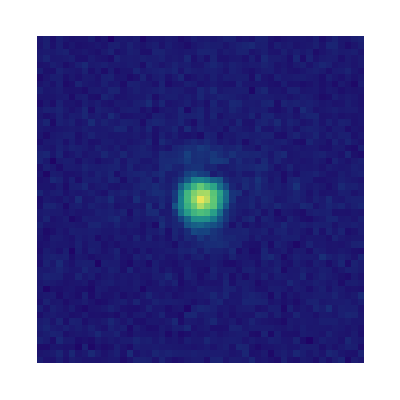

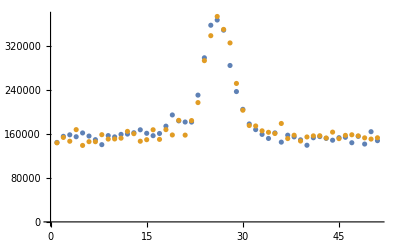

```mathematica
dataToFitTemp = dataTotal[[5]][[minX;;minX+900,minY;;minY+900]];
guess =Position[dataToFitTemp,Max[Flatten[dataToFitTemp]]];
Print[guess];
dataToFit = dataToFitTemp[[guess[[1,1]]-25;;guess[[1,1]]+25,guess[[1,2]]-25;;guess[[1,2]]+25]];
fitData4NoAngle[dataToFit,25,25, wGuess[[1]],wGuess[[2]]];
dataPoint = {wx,wy}/. fit["BestFitParameters"];
ArrayPlot[dataToFit,ColorFunction->"BlueGreenYellow"]
wx1d=fitDataSlicesArray[dataToFit,0][[1]];
xSlice = dataToFit1D;
wx1d=fitDataSlicesArray[dataToFit,1][[1]];
ySlice = dataToFit1D;
ListPlot[{xSlice,ySlice}, PlotRange-> All]
```

```mathematica
(.67)/(.55)330
```

402.

```mathematica
Mean[dataPoint*4.65/mag]
```

0.385429

```mathematica
simData =Import["A:\\heap\\Analysis_code\\Mathematica\\180313_simulatedPSF_OnCamera.tsv"];
```

```mathematica
bg=Mean[Transpose[dataToFit][[50]]]//N
bgSubMat = Table[bg, {i,1,51},{j,1,51}];
```

2571.24

```mathematica
dataToFitSub = dataToFit-bgSubMat;
```

```mathematica
normData=Total[Flatten[dataToFitSub]];
normSim=Total[Flatten[simData]];
```

```mathematica
simPSF=normData/normSim CenterArray[simData, {51,51}];
```

```mathematica
Max[dataToFitSub]/Max[simPSF]
```

0.383199

#### PSF at focus

```mathematica
Position[dataSet2,Max[Flatten[dataSet2]]]
```

{{}}

```mathematica
fit1=fitData4[dataToFit,25,25,4,4]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 38213.4 | 281.146 | 135.92 | 2.48761248579×10^-1182
wx | 4.24433 | 0.0314046 | 135.15 | 1.01687968316×10^-1176
wy | 4.26539 | 0.0315605 | 135.15 | 1.01687968105×10^-1176
θ | 0. | 1.76763×10^-18 | 0. | 1.
offset | 3102.07 | 15.0309 | 206.379 | 3.83153993215×10^-1612
x0 | 26.218 | 0.0156133 | 1679.2 | 4.7561802702×10^-3941
y0 | 26.0584 | 0.0156908 | 1660.75 | 1.31344951878×10^-3928

```mathematica
xp =x0/.fit["BestFitParameters"];
yp= y0/.fit["BestFitParameters"];
```

```mathematica
dataParsed = Flatten[Table[{{i-yp,j-xp},dataToFit[[i,j]]},{i,1,Dimensions[dataToFit][[1]]},{j,1,Dimensions[dataToFit][[1]]}],1];
```

```mathematica
dataInt = Interpolation[dataParsed]
```

InterpolatingFunction[{{-25.0584, 24.9416}, {-25.218, 24.782}}, <>]

```mathematica
pixSizeμm=4.65
```

4.65

```mathematica
nm=10^-9
```

1/1000000000

```mathematica
mag=52.7
```

52.7

```mathematica
resolution = 0.61/NA*461nm;

unPhotonDistribution[x_,y_, NA_] := (2BesselJ[1,((x^2+y^2)/((3.832^-1 resolution)^2))^(1/2)]/((x^2+y^2)/((3.832^-1 resolution)^2))^(1/2))^2;
```

```mathematica
aperture =350nm;
```

```mathematica
convolution[x_,y_, NA_] = Sum[If[(x0^2+y0^2)^(1/2)≤aperture/2,unPhotonDistribution[x-x0,y-y0, NA],0],{x0,-aperture/2,aperture/2,5nm},{y0,-aperture/2,aperture/2,5nm} ];
```

```mathematica
r
```

r

```mathematica
Clear[r]
```

```mathematica
rData =Table[{r*pixSizeμm/mag, 1/(2π*r)NIntegrate[r*dataInt[r*Cos[θ],r*Sin[θ]],{θ, 0,2π}]},{r,0,12,.4}];//Quiet
```

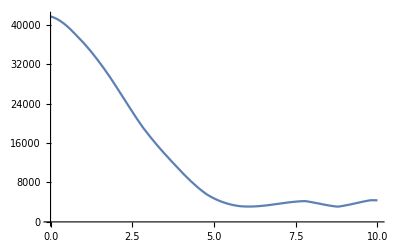

```mathematica
Plot[dataInt[0,x],{x,0,10}]
```

```mathematica
28μm/(1mm)//N
```

0.028

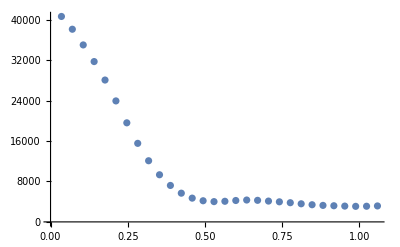

```mathematica
ListPlot[rData]
```

```mathematica
Clear[offsetbg]
```

```mathematica
psfParams = NonlinearModelFit[Drop[rData,1],A*convolution[r*μm,0,NA]+offsetbg,{{NA,.45},{A,20},{offsetbg,5000}},r]
psfParams["ParameterTable"]
```

FittedModel[3334.97+12.2667 ((1.27963×10^-13 («1»)^2)/(1/40000000000000000+(«1»)^2)+(«1»)/(«1»)+«1959»+(«24» («1»)^2)/(49/(«15»0)+(«1»)/(«13»)))]

| Estimate | Standard Error | t-Statistic | P-Value
NA | 0.58024 | 0.00407014 | 142.56 | 2.18857×10^-40
A | 12.2667 | 0.0831931 | 147.448 | 8.81747×10^-41
offsetbg | 3334.97 | 68.6186 | 48.6016 | 7.97507×10^-28

```mathematica
offsetD= 3334;
norm=psfParams[0.001]-offsetD;
```

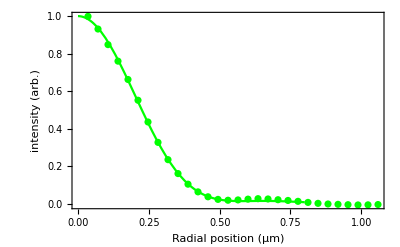

| Estimate | Standard Error | t-Statistic | P-Value
NA | 0.58024 | 0.00407014 | 142.56 | 2.18857×10^-40
A | 12.2667 | 0.0831931 | 147.448 | 8.81747×10^-41
offsetbg | 3334.97 | 68.6186 | 48.6016 | 7.97507×10^-28

```mathematica
lens2=Show[{Plot[(psfParams[x]-offsetD)/norm,{x,0,.8},PlotRange->All,PlotStyle-> Green],ListPlot[Map[{#[[1]],(#[[2]]-offsetD)/norm}&,rData],PlotStyle-> Green]}, FrameLabel-> {"Radial position (μm)", "intensity (arb.)"}, Axes-> False,Frame-> True]
psfParams["ParameterTable"]
```

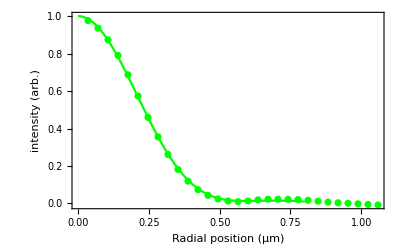

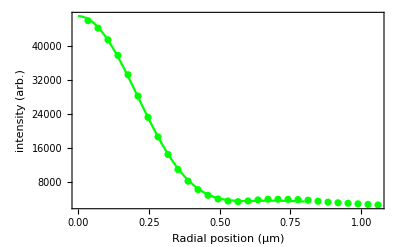
```mathematica
lens2 = -Graphics-;
```

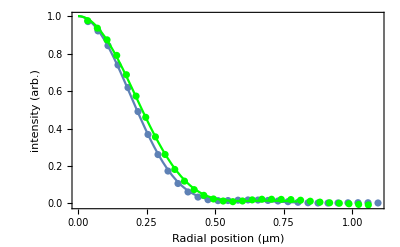

```mathematica
Show[{lens1,lens2}]
```

```mathematica
raDataInt = Interpolation[Transpose[{Transpose[rData][[1]],Transpose[rData][[2]]-709.05}]]
```

InterpolatingFunction[{{0., 1.05882}}, <>]

```mathematica
461*(.61)/(.62)
```

453.565

```mathematica
461*(.61)/(.68)
```

413.544

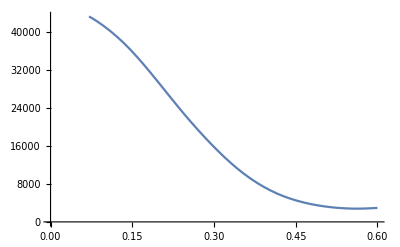

```mathematica
Plot[raDataInt[x],{x,0,.6}]
```

```mathematica
(Integrate[raDataInt[x],{x,0.08,.413}]/Integrate[raDataInt[x],{x,0.08,.8}])^2
```

0.728831

```mathematica
Integrate[raDataInt[x],{x,0.08,.8}]
```

9134.02

```mathematica
(7020/7281)^2//N
```

0.929592

#### Z scan

```mathematica
Dimensions[dataTotal[[1]]]
```

{1944,2592,3}

```mathematica
minX=50;
minY=50;
```

```mathematica
guess
```

{{499,578}}

```mathematica
keyVals
```

{0,1/400,11/4000,3/1000,1/4000,1/2000,3/4000,1/1000,1/800,3/2000,7/4000,1/500,9/4000}

```mathematica
dataList = {};
dataList1dx={};
dataList1dy={};
wGuess = {6,6};
minX=1;
minY=1;
Do[
dataCollapsed = funcBMP[dataTotal[[i]]];
dataToFitTemp =dataCollapsed[[minX;;minX+1900,minY;;minY+2500]];
guess =Position[dataToFitTemp,Max[Flatten[dataToFitTemp]]];
Print[guess];
guess = If[Length[guess]>1, {guess[[2]]}, guess];
dataToFit = dataToFitTemp[[guess[[1,1]]-10;;guess[[1,1]]+10,guess[[1,2]]-10;;guess[[1,2]]+10]];
fitData4[dataToFit,10,10, wGuess[[1]],wGuess[[2]]];
dataPoint = {wx,wy}/. fit["BestFitParameters"];
wx1d=fitDataSlicesArray[dataToFit,0][[1]];
wy1d=fitDataSlicesArray[dataToFit,1][[1]];
If[1<Norm[dataPoint]<200,wGuess=dataPoint];
AppendTo[dataList, {keyVals[[i]],dataPoint}];
AppendTo[dataList1dx, {keyVals[[i]],wx1d}];
AppendTo[dataList1dy, {keyVals[[i]],wy1d}];
Print[dataPoint]
,{i,1,Length[dataTotal]}]
```

{{431,1879}}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{19.1623,13.7334}

{{462,1764}}

{11.7747,11.7865}

{{348,1912}}

{9.12892,8.81671}

{{348,1912}}

{8.52742,8.14634}

{{497,1837},{498,1838}}

{8.20814,8.24133}

{{498,1836}}

{8.28283,8.42388}

{{350,1910}}

{8.36053,8.84589}

{{499,1835}}

{9.11605,9.57922}

{{498,1836}}

{10.0296,10.4178}

{{498,1836}}

{11.7459,11.8439}

{{498,1834}}

{14.2173,13.5521}

{{494,1834}}

{17.7571,16.3074}

{{495,1835}}

{26.7458,22.8022}

{{498,1834}}

{21.8515,21.2494}

{{1162,1},{1164,1},{1166,1},{1168,1}}

Part::take: Cannot take positions -9 through 11 in {9,8,9,8,9,9,9,8,8,8,8,8,9,9,9,8,9,9,8,9,9,9,9,8,8,9,9,8,9,9,9,9,9,8,9,9,9,8,8,9,9,8,8,8,9,8,9,8,9,9,«2451»}.

Set::shape: Lists {xdim,ydim} and {3} are not the same shape.

Part::partw: Part 4 of {{9,8,8,8,9,8,9,8,9,8,9,9,8,9,9,8,9,8,8,9,9,8,8,9,8,8,9,8,8,8,9,9,9,8,8,9,8,8,9,8,8,8,9,8,9,8,9,8,9,9,«2451»},{8,8,8,8,8,8,8,8,8,8,8,8,9,8,8,8,8,8,8,8,9,8,8,8,9,8,9,8,9,8,8,8,8,8,9,8,9,9,9,8,9,9,8,8,8,8,8,8,8,8,«2451»},«47»,{8,8,8,8,8,8,8,8,9,9,9,8,9,8,9,8,8,9,9,8,9,8,8,8,8,8,9,8,9,8,8,8,8,8,9,8,9,8,8,8,8,8,9,8,8,8,9,8,9,8,«2451»},«1851»}⟦1154;;1174,-9;;11⟧ does not exist.

Part::partw: Part 5 of {{9,8,8,8,9,8,9,8,9,8,9,9,8,9,9,8,9,8,8,9,9,8,8,9,8,8,9,8,8,8,9,9,9,8,8,9,8,8,9,8,8,8,9,8,9,8,9,8,9,9,«2451»},{8,8,8,8,8,8,8,8,8,8,8,8,9,8,8,8,8,8,8,8,9,8,8,8,9,8,9,8,9,8,8,8,8,8,9,8,9,9,9,8,9,9,8,8,8,8,8,8,8,8,«2451»},«47»,{8,8,8,8,8,8,8,8,9,9,9,8,9,8,9,8,8,9,9,8,9,8,8,8,8,8,9,8,9,8,8,8,8,8,9,8,9,8,8,8,8,8,9,8,8,8,9,8,9,8,«2451»},«1851»}⟦1154;;1174,-9;;11⟧ does not exist.

Part::partw: Part 6 of {{9,8,8,8,9,8,9,8,9,8,9,9,8,9,9,8,9,8,8,9,9,8,8,9,8,8,9,8,8,8,9,9,9,8,8,9,8,8,9,8,8,8,9,8,9,8,9,8,9,9,«2451»},{8,8,8,8,8,8,8,8,8,8,8,8,9,8,8,8,8,8,8,8,9,8,8,8,9,8,9,8,9,8,8,8,8,8,9,8,9,9,9,8,9,9,8,8,8,8,8,8,8,8,«2451»},«47»,{8,8,8,8,8,8,8,8,9,9,9,8,9,8,9,8,8,9,9,8,9,8,8,8,8,8,9,8,9,8,8,8,8,8,9,8,9,8,8,8,8,8,9,8,8,8,9,8,9,8,«2451»},«1851»}⟦1154;;1174,-9;;11⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

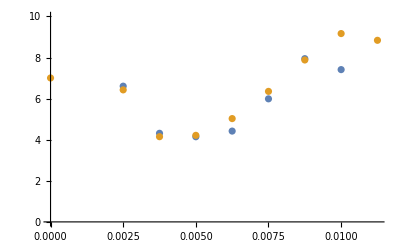

```mathematica
ListPlot[{dataList1dy,dataList1dx}, PlotRange-> {0,10}]
```

```mathematica
σyListUncal = MapThread[{#1,fitDataSlicesArray[#2,0][[1]]}&, {keyVals, dataTotal}];
```

$Aborted

```mathematica
datawx =Sort[Map[{#[[1]],2.65Abs[#[[2,1]]]μm}&, dataList]]//N
datawy = Sort[Map[{#[[1]],2.65Abs[#[[2,2]]]μm}&, dataList]]//N
```

{{0.,0.0000507802},{0.0025,0.0000312029},{0.00375,0.0000225977},{0.005,0.0000219495},{0.00625,0.0000241575},{0.0075,0.0000311268},{0.00875,0.0000470563},{0.01,0.0000708764},{0.01125,0.0000579064},{0.003 p5,0.0000241916},{0.00425 p5,0.0000217516},{0.0055 p5,0.0000221554},{0.00675 p5,0.0000265784},{0.008 p5,0.0000376758}}

{{0.,0.0000363936},{0.0025,0.0000312341},{0.00375,0.0000215878},{0.005,0.0000223233},{0.00625,0.0000253849},{0.0075,0.0000313862},{0.00875,0.0000432146},{0.01,0.0000604259},{0.01125,0.000056311},{0.003 p5,0.0000233643},{0.00425 p5,0.0000218395},{0.0055 p5,0.0000234416},{0.00675 p5,0.0000276073},{0.008 p5,0.000035913}}

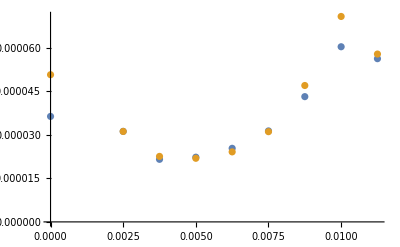

```mathematica
ListPlot[{datawy,datawx}]
```

```mathematica
nm=10^-9
```

1/1000000000

```mathematica
Sort[datawx//N]
```

{{0.009,0.0000458015},{0.01,0.0000318396},{0.011,0.0000211931},{0.012,0.0000196908},{0.013,0.000020277},{0.014,0.0000220296},{0.015,0.0000219979},{0.016,0.0000234709},{0.017,0.0000254924},{0.018,0.0000279163},{0.019,0.0000320319},{0.02,0.0000341236},{0.021,0.0000394932}}

```mathematica
fitfnX = NonlinearModelFit[Drop[Sort[datawx],-5], w(1+((z-z0x)/(π*w^2/(515nm)))^2)^(1/2),{{w,10μm},{z0x,1mm}},z];
fitfnX["BestFitParameters"]
fitfnX["ParameterTable"]
fitfnY = NonlinearModelFit[Drop[Sort[datawy],-5], w(1+((z-z0y)/(π*w^2/(515nm)))^2)^(1/2),{{w,10μm},{z0y,1mm}},z];
fitfnY["BestFitParameters"]
fitfnY["ParameterTable"]
```

{w→0.0000161376,z0x→0.00466298}

| Estimate | Standard Error | t-Statistic | P-Value
w | 0.0000161376 | 1.42126×10^-6 | 11.3544 | 9.20776×10^-6
z0x | 0.00466298 | 0.000346749 | 13.4477 | 2.95055×10^-6

{w→0.0000207627,z0y→0.00406668}

| Estimate | Standard Error | t-Statistic | P-Value
w | 0.0000207627 | 1.7504×10^-6 | 11.8616 | 6.87268×10^-6
z0y | 0.00406668 | 0.000351192 | 11.5797 | 8.07439×10^-6

```mathematica
nm=10^-9
```

1/1000000000

```mathematica
fitfnX = NonlinearModelFit[Drop[Sort[datawx],-5], w(1+((z-z0x)/z0)^2)^(1/2),{{w,5μm},{z0x,1000μm},{z0,1000μm}},z];
fitfnX["BestFitParameters"]
fitfnX["ParameterTable"]
fitfnY = NonlinearModelFit[Drop[Sort[datawy],-5], w(1+((z-z0y)/z0)^2)^(1/2),{{w,5μm},{z0y,1000μm},{z0,1000μm}},z];
fitfnY["BestFitParameters"]
fitfnY["ParameterTable"]
```

{w→0.0000209569,z0x→0.00468445,z0→0.00211195}

| Estimate | Standard Error | t-Statistic | P-Value
w | 0.0000209569 | 4.46367×10^-6 | 4.69499 | 0.00334347
z0x | 0.00468445 | 0.000379601 | 12.3405 | 0.0000172679
z0 | 0.00211195 | 0.00058229 | 3.62696 | 0.011005

{w→0.0000220302,z0y→0.00414649,z0→0.0027619}

| Estimate | Standard Error | t-Statistic | P-Value
w | 0.0000220302 | 2.88367×10^-6 | 7.63966 | 0.000262522
z0y | 0.00414649 | 0.000393289 | 10.5431 | 0.0000428074
z0 | 0.0027619 | 0.000531309 | 5.19828 | 0.00201819

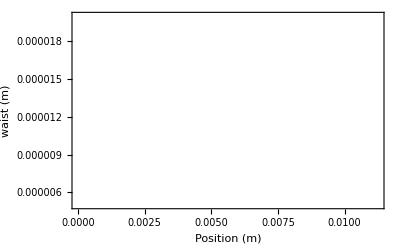

Astigmatism: -0.220756

| Estimate | Standard Error | t-Statistic | P-Value
w | 0.0000220302 | 2.88367×10^-6 | 7.63966 | 0.000262522
z0y | 0.00414649 | 0.000393289 | 10.5431 | 0.0000428074
z0 | 0.0027619 | 0.000531309 | 5.19828 | 0.00201819

| Estimate | Standard Error | t-Statistic | P-Value
w | 0.0000209569 | 4.46367×10^-6 | 4.69499 | 0.00334347
z0x | 0.00468445 | 0.000379601 | 12.3405 | 0.0000172679
z0 | 0.00211195 | 0.00058229 | 3.62696 | 0.011005

```mathematica
Show[{Plot[{fitfnX[z],fitfnY[z]},{z,0.000,.005}],ListPlot[{datawx,datawy}]}, PlotRange-> {5μm,20μm}, Frame-> True, Axes-> False, FrameLabel-> {"Position (m)","waist (m)"}]
Print["Astigmatism: ", ((z0y-z0x)/.Join[fitfnY["BestFitParameters"],fitfnX["BestFitParameters"]])/(Mean[{(z0/.fitfnX["BestFitParameters"]),z0/.fitfnY["BestFitParameters"]}])]
fitfnY["ParameterTable"]
fitfnX["ParameterTable"]
```

```mathematica
7*3
```

21

```mathematica
Solve[fitfnX[z]==fitfnY[z],z]
```

{{z→0.000337883},{z→0.0177153}}

```mathematica
fitfnX[0.00033788315042453034]
fitfnX[0.00020595223984501754]
fitfnX[0.00033788315042453034]/fitfnX[0.00020595223984501754]
```

9.89566×10^-6

9.80562×10^-6

1.00918

```mathematica
fitfnY[0.00033788315042453034]
fitfnY[0.000588996428325959]
fitfnY[0.00033788315042453034]/fitfnY[0.000588996428325959]
```

9.89566×10^-6

9.55017×10^-6

1.03618

```mathematica
6.45/7.05
```

0.914894